```mathematica
DiMauro={{0.11592770333719869 ,1.430902724036737*10^-7 },{0.1552419727919801,1.3179420496721543*10^-7},{0.20454943547538015,8.583697005721025*10^-8},{0.2761483125230999,9.429532155412788*10^-8},{0.36803607894880785,1.5174694782872762*10^-7},{0.48679704343252744,2.3027136175334634*10^-7},{0.6526663609063482,2.762615710198307*10^-7},{0.868657027321059,3.2949591880051146*10^-7},{1.164235975134054,3.6624168819479853*10^-7},{1.5487794318504893,3.9298828318905065*10^-7},{2.073515175360936,3.4332619284070296*10^-7},{2.756110370684767,3.0707058382385326*10^-7},{3.6645869109432856,2.9470080134723354*10^-7},{4.938211547069397,2.15863437995542*10^-7},{6.609896317259527,1.7992791265356413*10^-7},{8.653956168958699,1.4393323808133127*10^-7},{11.585659239935609,1.250078960579582*10^-7},{15.282166070975402,1.0358715668866392*10^-7},{20.457126458496873,8.787762697302056*10^-8},{27.388854044575474,7.722477322409351*10^-8},{36.36344700262212,5.3653189668710636*10^-8},{48.734279516882474,5.8940160269446834*10^-8},{65.21964092744737,4.714914987619674*10^-8},{86.75685271001828,5.000157918665334*10^-8}};
Zhong12={{0.2698936461850911,2.0235896477251556*10^-8},{0.4031852049908963,5.55773658648687*10^-8},{0.5306041497635453,8.286427728546843*10^-8},{0.6836949708649847,9.319395762340776*10^-8},{0.8809558187480787,7.722449945836255*10^-8},{1.1593649950439693,1.2067926406393264*10^-7},{1.493866975713819,1.2949258422052604*10^-7},{1.965974958149487,1.52641796717523*10^-7},{2.5332014314857654,1.4563484775012414*10^-7},{3.3337711183217964,1.5627069765469932*10^-7},{4.205844492778353,1.4563484775012414*10^-7},{7.284258025108297,8.68511373751352*10^-8},{51.951289318465555;3.23745754281764*10^-8}};
Zhong1={{0.2756556969794437;2.5595479226995333*10^-8},{0.41179294238496555;7.906043210907701*10^-8},{0.5306041497635453;1.2648552168552957*10^-7},{0.6836949708649847;1.5998587196060571*10^-7},{0.8809558187480787;1.389495494373136*10^-7},{1.1593649950439693;1.8420699693267125*10^-7},{1.525760047357919;1.8858632787726476*10^-7},{1.965974958149487;1.9765980717016307*10^-7},{2.5332014314857654;1.7575106248547896*10^-7},{3.3337711183217964;1.8858632787726476*10^-7},{4.295636490267305;1.7992936232915516*10^-7},{7.439772114947442;1.0730309405261565*10^-7},{51.951289318465555;3.906939937054621*10^-8}};

(*We want to interpolate using the following function*)
```

{3.57726×10^-8,3.29486×10^-8,2.14592×10^-8,2.35738×10^-8,3.79367×10^-8,5.75678×10^-8,6.90654×10^-8,8.2374×10^-8,9.15604×10^-8,9.82471×10^-8,8.58315×10^-8,7.67676×10^-8,7.36752×10^-8,5.39659×10^-8,4.4982×10^-8,3.59833×10^-8,3.1252×10^-8,2.58968×10^-8,2.19694×10^-8,1.93062×10^-8,1.34133×10^-8,1.4735×10^-8,1.17873×10^-8,1.25004×10^-8}

FittedModel[9.38198×10^-8 (Piecewise[{{2.79056 x^0.58, x<2.06}, {6.69069/x^0.63, x>2.06}, {0, True}}])]

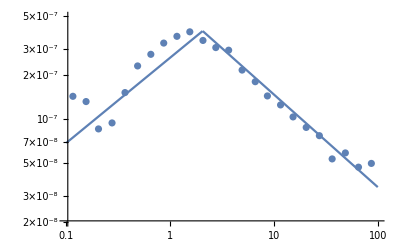

```mathematica
POINTS
PointsErrors=POINTS . {0,0.25}
Eb=2.06 GeV;
n1=1.42;
n2=2.63;
GeV=1; (*GeV=0.00160218 erg*)

Clear[F1,F];
F[x_]=Piecewise[{{x^2 (x/Eb)^-n1,x<Eb},{x^2 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[POINTS,F0  F[x],F0,x,Weights->1/PointsErrors^2]
(*F1[x_]=Fit[DiMauro,F[x],x]*)

Show[ListLogLogPlot[POINTS,PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}]]
```

```mathematica
NIntegrate[F1[x]/x^2,{x,0.1,100}] 0.00160218
```

2.07929×10^-9

FittedModel[Piecewise[{{2.96402×10^-7 x^0.378373, x<1.98152}, {(5.89005×10^-7)/x^0.625804, x>1.98152}, {0, True}}]]

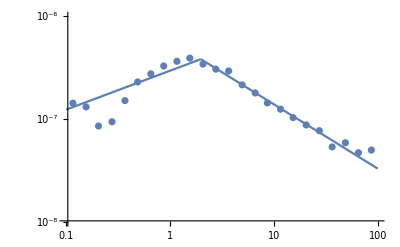

```mathematica
Clear[F0,n1,n2,Eb];
F[x_]=  Piecewise[{{x^2  F0 (x/Eb)^-n1,x<Eb},{x^2 F0 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[DiMauro,{F[x],Eb>0},{F0,{n1,1.41},{n2,2.63},{Eb,2.06}},x]
Show[ListLogLogPlot[DiMauro,PlotRange->{{10^-1,10^2},{10^-8,10^-6}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{10^-8,10^-6}}]]
```

FittedModel[Piecewise[{{2.94163×10^-7 x^0.455388, x<2.06}, {(6.68131×10^-7)/x^0.679722, x>2.06}, {0, True}}]]

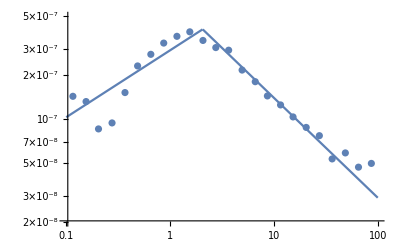

3.92597×10^-7 (Piecewise[{{0.743557 x^0.41, x<2.06}, {1.57665/x^0.63, x>2.06}, {0, True}}])

```mathematica
Clear[F0,n1,n2];
Eb=2.06;
F[x_]=Piecewise[{{x^2  F0 (x/Eb)^-n1,x<Eb},{x^2  F0 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[DiMauro,F[x],{F0,n1,n2},x]
Show[ListLogLogPlot[DiMauro,PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}]]
```